```mathematica
Solve[(X+1)P==X^2-1,P]
```

{{P→-1+X}}

```mathematica
Solve[P'*(X^2)==3X*P,P]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[X^2 P'==3 P X,P]

```mathematica
Solve[P'*X==3*P,P]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[X P'==3 P,P]

```mathematica
Reduce[P'*(X^2)==3X*P]
```

(P'≠0&&X==(3 P)/P')||P==0||X==0

```mathematica
DSolve[{X^2 P'[X]==3 X P[X]},P[X],X]
```

{{P[X]→X^3 C[1]}}

```mathematica
Solve[X^2*P'==3 P*X,P,MaxExtraConditions->Automatic]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[X^2 P'==3 P X,P,MaxExtraConditions→Automatic]

```mathematica
VectorPlot[{1,(3 P)/X},{X,0,6},{P,0,6},VectorStyle->"Segment"]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

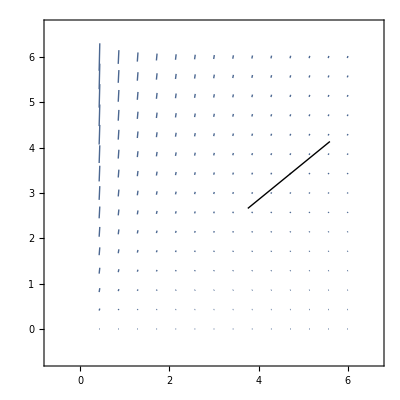

```mathematica
DSolve[{P[X]*P''[X]==X*P'[X]},P[X],X]
```

DSolve[{P[X] P''[X]==X P'[X]},P[X],X]

```mathematica
DSolve[{X^2 P'[X]==3 X P[X]},P[X],X]
```

{{P[X]→X^3 C[1]}}

```mathematica
DSolve[P[X] P''[X]==X P'[X],{P[X],P[X]},{X}]
```

DSolve[P[X] P''[X]==X P'[X],{P[X],P[X]},{X}]

```mathematica
DSolve[P[P[X]]==P[X],P[X],X]
```

DSolve::nestdv: The expression P[X] has nested dependent variables.

DSolve[P[P[X]]==P[X],P[X],X]

```mathematica
DSolve[P@*P@X==P[X],P[X],X]
```

DSolve::nestdv: The expression P[X] has nested dependent variables.

DSolve[P[P[X]]==P[X],P[X],X]

```mathematica
(-1)!
```

ComplexInfinity

```mathematica
Factorial[-1]
```

ComplexInfinity

```mathematica
FullForm[ComplexInfinity]
```

DirectedInfinity[]

```mathematica
Binomial[i,-1]
```

0

```mathematica
P=X-2
```

-2+X

```mathematica
Expand[P^2-2]
```

2-4 X+X^2

```mathematica
Expand[P^3-2]
```

-10+12 X-6 X^2+X^3

```mathematica
Clear[P]
Expand[RecurrenceTable[{P[n+1]==P[n]^2-2,P[1]==(X-2)},P,{n,1,5}]]
```

{-2+X,2-4 X+X^2,2-16 X+20 X^2-8 X^3+X^4,2-64 X+336 X^2-672 X^3+660 X^4-352 X^5+104 X^6-16 X^7+X^8,2-256 X+5440 X^2-45696 X^3+201552 X^4-537472 X^5+940576 X^6-1136960 X^7+980628 X^8-615296 X^9+283360 X^10-95680 X^11+23400 X^12-4032 X^13+464 X^14-32 X^15+X^16}

```mathematica
Table[CoefficientList[P,X][[1;;Min[Length[P],3]]],{P,Expand[RecurrenceTable[{P[n+1]==P[n]^2-2,P[1]==(X-2)},P,{n,1,10}]]}]
```

{{-2,1},{2,-4,1},{2,-16,20},{2,-64,336},{2,-256,5440},{2,-1024,87296},{2,-4096,1397760},{2,-16384,22368256},{2,-65536,357908480},{2,-262144,5726601216}}

```mathematica
Length[{-2,1,3}]
```

3

```mathematica
FindSequenceFunction[{-4,-16,-64,-256,-1024,-4096,-16384},n]
```

-4^n

```mathematica
FindSequenceFunction[{1,20,336,5440,87296,1397760,22368256,357908480,5726601216},n]
```

1/3 4^(-1+n) (-1+4^n)

```mathematica
Table[1/3 4^(-1+n) (-1+4^n),{n,1,10}]
```

{1,20,336,5440,87296,1397760,22368256,357908480,5726601216,91625881600}

```mathematica
Table[4^(n-1)/3*(4^(n-1)-1)+4^(2n-2),{n,1,10}]
Table[4^(n-1)/3*(4^(n-1)-1)+4^(n-1)*4^(n-1),{n,1,10}]
Table[4^(n-1)/3*(4^(n-1)-1)+4^(n-1)*4^(n-1),{n,1,10}]
```

{1,20,336,5440,87296,1397760,22368256,357908480,5726601216,91625881600}

{1,20,336,5440,87296,1397760,22368256,357908480,5726601216,91625881600}

```mathematica
Table[4^(n-1)/3*(4^n-1),{n,1,10}]
```

{1,20,336,5440,87296,1397760,22368256,357908480,5726601216,91625881600}

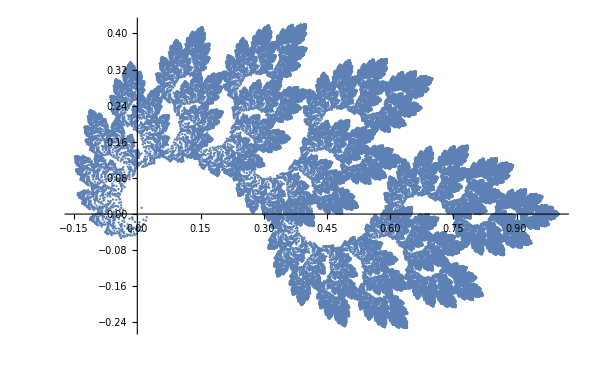

```mathematica
a=.7+.3I;b=0;c=0;d=.6;e=Conjugate;f@z_:={a z+b e@z,c (z-1)+d(e@z-1)+1};ListPlot[ReIm@#&/@Nest[Flatten[f@#&/@#]&,{1+.9I},16]]
```

```mathematica
Show[ExampleData[{"Geometry3D","Torus"}]]
```

-Graphics3D-

```mathematica
ExampleData["Geometry3D"]
```

{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}}

```mathematica
Table[4^(n-1)*2,{n,1,10}]
```

{2,8,32,128,512,2048,8192,32768,131072,524288}

```mathematica
Table[4^n-1,{n,1,10}]
```

{3,15,63,255,1023,4095,16383,65535,262143,1048575}